# DATI DEL SISTEMA PROPRIO LTI-TD

```mathematica
ClearAll["Global`*"]
```

```mathematica
A = {{1/2,-1/2,1/2}, {1/2,-1/2,-1/2}, {5/16,-11/48,1/6}}; A//MatrixForm
```

(1/2 | -1/2 | 1/2
1/2 | -1/2 | -1/2
5/16 | -11/48 | 1/6)

```mathematica
B = {{0}, {0}, {-1}}; B//MatrixForm
```

(0
0
-1)

```mathematica
Subscript[C, 1] = {-7/4, 9/4, 0}; Subscript[C, 1]//MatrixForm
```

(-7/4
9/4
0)

## 1. Studio dei modi naturali del sistema

```mathematica
λ = Eigenvalues[A]
```

{2/3,-1/4,-1/4}

```mathematica
NullSpace[A+1/4IdentityMatrix[3]]
```

{{6,10,1}}

```mathematica
{T,Λ} = JordanDecomposition[A]
```

{{{6,56,15/8},{10,72,3/8},{1,0,1}},{{-1/4,1,0},{0,-1/4,0},{0,0,2/3}}}

```mathematica
T//MatrixForm
```

(6 | 56 | 15/8
10 | 72 | 3/8
1 | 0 | 1)

```mathematica
Λ//MatrixForm
```

(-1/4 | 1 | 0
0 | -1/4 | 0
0 | 0 | 2/3)

```mathematica
MatrixPower[Λ,k]//MatrixForm
```

((-1/4)^k | -(-1)^k 4^(1-k) k | 0
0 | (-1/4)^k | 0
0 | 0 | (3/2)^-k)

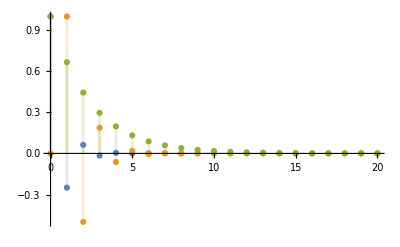

```mathematica
DiscretePlot[{(-1/4)^k,-(-1)^k 4^(1-k) k,(3/2)^-k},{k,0,20}, PlotRange->All]
```

## 2. Calcolo della risposta libera

```mathematica
Subscript[x, 0]={{3},{-2},{-3}}; Subscript[x, 0]//MatrixForm
```

(3
-2
-3)

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{-335/121},{63/176},{-28/121}}

```mathematica
Subscript[x, l][k_] :=Simplify[T.MatrixPower[Λ,k].Subscript[x, 0]]
```

```mathematica
Subscript[x, l][k]//MatrixForm
```

(2^(-3-2 k) 3^-k (-752 (-3)^k-45 8^k+128 (-1)^k 3^(1+k) k)
2^(-3-2 k) 3^-k (-3 (304 (-3)^k+3 8^k)+640 (-3)^k k)
12^-k (3 ((-3)^k-8^k)+8 (-3)^k k))

```mathematica
Subscript[Y, l][k_] :=Simplify[Subscript[C, 1].Subscript[x, l][k]]
```

Grafico della risposta libera

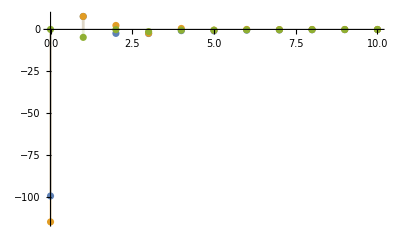

```mathematica
DiscretePlot[({{2^(-3-2 k) 3^-k (-752 (-3)^k-45 8^k+128 (-1)^k 3^(1+k) k)}, {2^(-3-2 k) 3^-k (-3 (304 (-3)^k+3 8^k)+640 (-3)^k k)}, {12^-k (3 ((-3)^k-8^k)+8 (-3)^k k)}}),{k,0,10},PlotRange->All]
```

Le componenti dello stato avranno questo andamento:

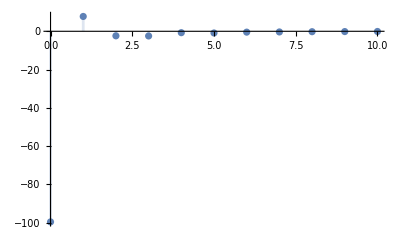

```mathematica
DiscretePlot[Evaluate[Subscript[x, l][k][[1]]], {k,0,10},PlotRange->All]
```

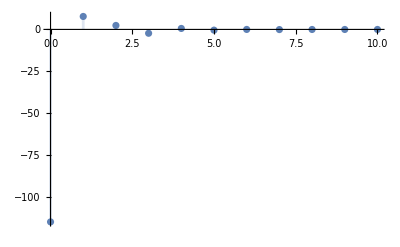

```mathematica
DiscretePlot[Evaluate[Subscript[x, l][k][[2]]], {k,0,10},PlotRange->All]
```

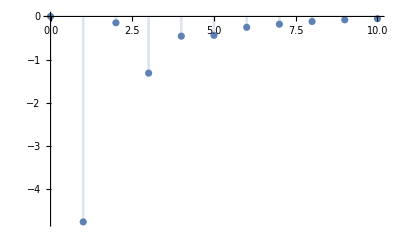

```mathematica
DiscretePlot[Evaluate[Subscript[x, l][k][[3]]], {k,0,10},PlotRange->All]
```

Grafico dell’uscita

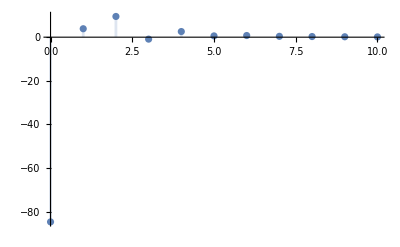

```mathematica
DiscretePlot[Subscript[Y, l][k], {k,0,10},PlotRange->All]
```

## 3. Studio della configurazione degli stati iniziali che attivano sulla risposta libera alcuni modi naturali e altri no

```mathematica
Subscript[x, 01]= Transpose[T][[1]]
```

{6,10,1}

```mathematica
Subscript[z, 01]=Inverse[T].Subscript[x, 01]
```

{1,0,0}

```mathematica
Subscript[x, 02]= Transpose[T][[2]]
```

{56,72,0}

```mathematica
Subscript[z, 02]=Inverse[T].Subscript[x, 02]
```

{0,1,0}

```mathematica
Subscript[x, 03]= Transpose[T][[3]]
```

{15/8,3/8,1}

```mathematica
Subscript[z, 03]=Inverse[T].Subscript[x, 03]
```

{0,0,1}

## 4. La funzione di trasferimento del sistema, i suoi poli e zeri

```mathematica
G[z_]:=Simplify[Subscript[C, 1].Inverse[z IdentityMatrix[3]-A].B][[1]]
```

```mathematica
G[z]
```

(12 (-1+8 z))/((-2+3 z) (1+4 z)^2)

```mathematica
Factor[CharacteristicPolynomial[A,z]]
```

-1/48 (-2+3 z) (1+4 z)^2

```mathematica
Factor[Denominator[G[z]]]
```

(-2+3 z) (1+4 z)^2

```mathematica
Solve[Denominator[G[z]]== 0,z]
```

{{z→-1/4},{z→-1/4},{z→2/3}}

```mathematica
Solve[Numerator[G[z]]==0, z]
```

{{z→1/8}}

## 5. Risposta al gradino e il suo grafico

```mathematica
Subscript[Y, f][z_]:=G[z] ZTransform[UnitStep[k],k,z]
```

```mathematica
Subscript[Y, f][z][[1]]//Apart
```

12

```mathematica
Subscript[Y, f][z]/z
```

(12 (-1+8 z))/((-1+z) (-2+3 z) (1+4 z)^2)

```mathematica
Apart[Subscript[Y, f][z]/z]
```

84/(25 (-1+z))-1404/(121 (-2+3 z))-576/(55 (1+4 z)^2)+6144/(3025 (1+4 z))

```mathematica
Subscript[Y, f2][z_]:=(Subscript[D, 1](1/(z-1))+Subscript[D, 2](1/(z-2/3))+Subscript[D, 3](1/(z+1/4)^2)+Subscript[D, 4](1/(z+1/4)))z
```

```mathematica
Subscript[D, 1]=lim_(z->1) (z-1)((Subscript[Y, f][z])/z)
```

84/25

Un altro modo per calcolare D_1 è il seguente:
D_1 =G[1]

```mathematica
G[1]
```

84/25

```mathematica
Subscript[D, 2]=lim_(z->2/3) (z-2/3)((Subscript[Y, f][z])/z)
```

-468/121

```mathematica
Subscript[D, 3]=lim_(z->-1/4) D[(z+1/4)^2((Subscript[Y, f][z])/z),z]
```

1536/3025

```mathematica
Subscript[D, 4]=lim_(z->-1/4) (z+1/4)^2((Subscript[Y, f][z])/z)
```

-36/55

Scrivo Y[z] moltiplicando a destra e sinistra per z:

```mathematica
Subscript[D, 1](z/(z-1))+ Subscript[D, 2](z/(z-2/3))+ Subscript[D, 3](z/(z+1/4)^2)+ Subscript[D, 4](z/(z+1/4))
```

(84 z)/(25 (-1+z))-(468 z)/(121 (-2/3+z))+(1536 z)/(3025 (1/4+z)^2)-(36 z)/(55 (1/4+z))

```mathematica
Subscript[Y, f2][z]
```

z (84/(25 (-1+z))-468/(121 (-2/3+z))+1536/(3025 (1/4+z)^2)-36/(55 (1/4+z)))

Scrivo ora la risposta forzata nel dominio del tempo

```mathematica
Subscript[y, f][k_]:=Expand[InverseZTransform[Subscript[Y, f2][z],z,k]]UnitStep[k]
```

```mathematica
Subscript[y, f][k]
```

(84/25-13/121 2^(2+k) 3^(2-k)-9/55 (-1)^k 4^(1-k)-(3 (-1)^k 2^(11-2 k) k)/3025) UnitStep[k]

Grafico componente a regime e transitoria

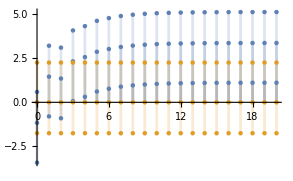

```mathematica
DiscretePlot[{Subscript[y, f][k]-Subscript[C, 1],Subscript[C, 1]}, {k,0,20}, PlotRange->All]
```

Grafico risposta forzata

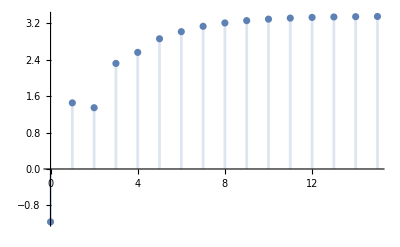

```mathematica
DiscretePlot[Subscript[y, f][k], {k,0,15}, PlotRange->All]
```

grafico risposta al gradino unitario

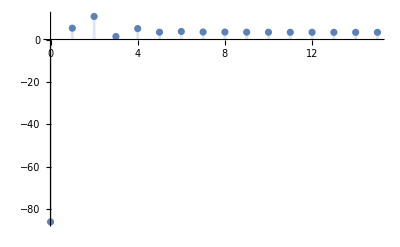

```mathematica
DiscretePlot[Subscript[y, f][k]+Subscript[Y, l][k], {k,0,15}, PlotRange->All]
```

## 6. I suoi modelli ARMA equivalenti, individuando le condizionali iniziali all’uscita compatibili con lo stato iniziale

Prendiamo in considerazione le condizioni iniziali:

```mathematica
condInizialiARMA = {{-3},{0},{-2}}
```

{{-3},{0},{-2}}

```mathematica
eqArma =Expand[Y[z]Denominator[G[z]]==U[z]Numerator[G[z]]]
```

-2 Y[z]-13 z Y[z]-8 z^2 Y[z]+48 z^3 Y[z]==-12 U[z]+96 z U[z]

```mathematica
eqDiff = InverseZTransform[eqArma, z, k] /. {Y[z]-> ZTransform[y[k], k,z], U[z]-> ZTransform[u[k], k, z]}/.{InverseZTransform[z ZTransform[y[k],k,z],z,k]->y[k+1],
InverseZTransform[z^2 ZTransform[y[k],k,z],z,k]->y[k+2],
InverseZTransform[z^3 ZTransform[y[k],k,z],z,k]->y[k+3],
InverseZTransform[z ZTransform[u[k],k,z],z,k]->u[k+1]}
```

-2 y[k]-13 y[1+k]-8 y[2+k]+48 y[3+k]==-12 u[k]+96 u[1+k]

```mathematica
eqDiff2 = ZTransform[eqDiff, k, z] /. {ZTransform[y[k], k, z] -> Y[z], ZTransform[u[k], k, z] -> U[z]}
```

-2 Y[z]-13 (-z y[0]+z Y[z])-8 (-z^2 y[0]-z y[1]+z^2 Y[z])+48 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 Y[z])==-12 U[z]+96 (-z u[0]+z U[z])

```mathematica
rispostaForzataLibera = Collect[Solve[eqDiff2, Y[z]][[1,1]][[2]], U[z]]
```

((-12+96 z) U[z])/((-2+3 z) (1+4 z)^2)+(-96 z u[0]-13 z y[0]-8 z^2 y[0]+48 z^3 y[0]-8 z y[1]+48 z^2 y[1]+48 z y[2])/((-2+3 z) (1+4 z)^2)

```mathematica
Subscript[Y, armaforzata][z_]:=rispostaForzataLibera[[1]]
```

```mathematica
Subscript[Y, armaforzata][z]
```

((-12+96 z) U[z])/((-2+3 z) (1+4 z)^2)

```mathematica
Subscript[Y, armalibera][z_]:=(rispostaForzataLibera[[2]]/.{y[0]->Subscript[C, 1].condInizialiARMA, y[1]->Subscript[C, 1].A.condInizialiARMA,y[2]->Subscript[C, 1].A.A.condInizialiARMA})[[1,1]]
Subscript[Y, armalibera][z]
```

1/(-2+3 z)

```mathematica
Subscript[y, armaLibera][k_]:=Expand[InverseZTransform[Subscript[Y, armalibera][z],z,k]]
Subscript[y, armaLibera][k]
```

2^(-1+k) 3^-k UnitStep[-1+k]

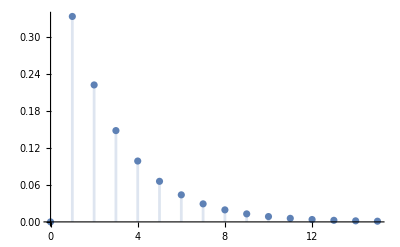

```mathematica
DiscretePlot[Subscript[y, armaLibera][k],{k,0,15},PlotRange->All]
```

```mathematica
Subscript[u, gT][k_]:=Piecewise[{{1, 0<=k<=10}, {0, k>10}, {0, k<0}}]
```

```mathematica
Subscript[U, gT][z_]:=ZTransform[Subscript[u, gT][k], k, z]
```

```mathematica
Subscript[U, gT][z]
```

(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)/z^10

```mathematica
Subscript[Y, forgT][z_]:=Subscript[Y, armaforzata][z]/.U[z]->Subscript[U, gT][z]
```

```mathematica
Subscript[Y, forgT][z]
```

((-12+96 z) (1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10))/(z^10 (-2+3 z) (1+4 z)^2)

Ritornando al dominio della variabile k:

```mathematica
Subscript[y, forgT][k_]:=FullSimplify[Expand[InverseZTransform[Subscript[Y, forgT][z],z,k]]]
```

```mathematica
Subscript[y, forgT][k]
```

Piecewise[{{2, k==2}, {25/12, k==3}, {95/36, k==4}, {4903/1728, k==5}, {31357/10368, k==6}, {779461/248832, k==7}, {1197907/373248, k==8}, {116786563/35831808, k==9}, {707954635/214990848, k==10}, {1/121 2^(-9-2 k) (2276287 3^(2-k) 8^k+24576 (-1)^k (-299137760+27682413 k)), k>10}, {0, True}}]

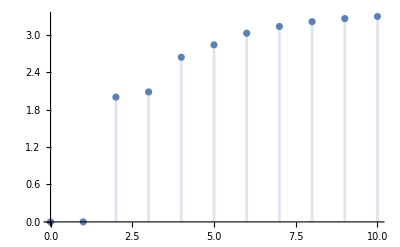

```mathematica
DiscretePlot[Piecewise[{{2, k==2}, {25/12, k==3}, {95/36, k==4}, {4903/1728, k==5}, {31357/10368, k==6}, {779461/248832, k==7}, {1197907/373248, k==8}, {116786563/35831808, k==9}, {707954635/214990848, k==10}, {1/121 2^(-9-2 k) (2276287 3^(2-k) 8^k+24576 (-1)^k (-299137760+27682413 k)), k>10}, {0, True}}], {k, 0, 10}, PlotRange->All]
```

```mathematica
g[k_]:=InverseZTransform[G[z],z,k]
```

```mathematica
g[k]
```

1/121 2^(1-2 k) 3^(1-k) (-160 (-3)^k+39 2^(3 k)+88 (-1)^k 3^(1+k) k) (1-UnitStep[-k])

```mathematica
sommaConvoluzione[k_]:=∑_(i=0)^k g[i]Subscript[u, gT][i]
```

```mathematica
sommaConvoluzione[k]
```

Piecewise[{{707954635/214990848, k>10}, {(12^(1-k) (128 (-3)^k-975 8^k+847 12^k+220 (-1)^k 3^(1+k) k))/3025, 0<k≤10}, {0, True}}]

```mathematica
DiscretePlot[sommaConvoluzione[k], {k, 0, 10}, PlotRange->All]
```

-Graphics-

L’uscita complessiva

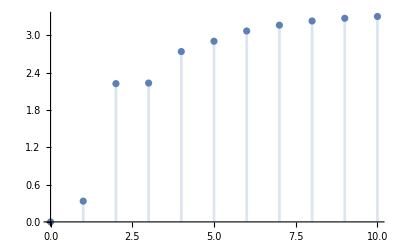

```mathematica
DiscretePlot[Subscript[y, armaLibera][k]+sommaConvoluzione[k], {k, 0, 10}, PlotRange->All]
```

## 7. determinare, sul modello ARMA apposito, le condizioni iniziali tali che la risposta al gradino coincide conil suo valore di regime

```mathematica
Subscript[v, 0]={{Subscript[v, 1]},{Subscript[v, 2]},{Subscript[v, 3]}}
```

{{v_1},{v_2},{v_3}}

```mathematica
Subscript[Y, liberaPunto7]=(rispostaForzataLibera[[2]]/.{y[0]-> Subscript[C, 1].Subscript[v, 0],y[1]-> Subscript[C, 1].A.Subscript[v, 0],y[2]->Subscript[C, 1].A.A.Subscript[v, 0]})[[1]]
```

1/((-2+3 z) (1+4 z)^2)(-13 z (-(7 v_1)/4+(9 v_2)/4)-8 z^2 (-(7 v_1)/4+(9 v_2)/4)+48 z^3 (-(7 v_1)/4+(9 v_2)/4)-8 z (v_1/4-v_2/4-2 v_3)+48 z^2 (v_1/4-v_2/4-2 v_3)+48 z (-(5 v_1)/8+(11 v_2)/24-v_3/12)-96 z u[0])

```mathematica
Subscript[rispostaForzataz, g]=rispostaForzataLibera[[1]]/.U[z]->z/(z-1)
```

(z (-12+96 z))/((-1+z) (-2+3 z) (1+4 z)^2)

```mathematica
componenteRegime[k_]:=∑_(i=0)^∞ g[i]
```

```mathematica
componenteRegime[k]
```

84/25

```mathematica
componenteTransitoria=Factor[Subscript[rispostaForzataz, g]-ZTransform[componenteRegime[k],k,z]]
```

-(12 z (-11+280 z+336 z^2))/(25 (-2+3 z) (1+4 z)^2)

```mathematica
zer = Factor[componenteTransitoria+Subscript[Y, liberaPunto7]]
```

-((z (-528+13440 z+16128 z^2+925 v_1-2600 z v_1+8400 z^2 v_1+525 v_2+3000 z v_2-10800 z^2 v_2-1200 v_3+9600 z v_3+9600 u[0]))/(100 (-2+3 z) (1+4 z)^2))

```mathematica
Solve[CoefficientList[Numerator[Simplify[Expand[zer]]],z] == {0,0,0},{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]}]
```

{}